```mathematica
constants = {b-> 1 (*T*), u0 -> 100000(*V*), c-> 300000000(*m/s*), q-> 1.602*10^-19(*C*), m -> 1.673*10^-27(*kg*)}
```

{b→1,u0→100000,c→300000000,q→1.602×10^-19,m→1.673×10^-27}

Formeln:

Zyklotronfrequenz

```mathematica
ωc=(q*b)/m //.constants;
```

Versuche ein Modul zu erstellen...

```mathematica
blub[{w_, r_, ϕ_, ωrf_, n_}] := Module[{γ, uhf,ϕ2, w2,radius,vmom},
ϕ2 =ϕ + (ωrf*γ*(Pi/ωc)-Pi)//.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]];(* Formel vom Übungsblatt*)
uhf = -u0 Cos[ωrf*Pi*(γ/ωc) + ϕ]//.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]]; (* momentane Beschleunigungsspannung. Eigentlich sollte es reichen, Cos[ϕ] zu nehmen -- Du darfst hier nicht ϕ2 einsetzten, sondern du musst nur Pi*γ2 einsetzten, da du *)
w2 = w + uhf//.constants;
vmom:=√((2/m)*w); (* oder w2?*)
radius = (γ*vmom*m)/(q*b) //.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]]//.constants(*später -- Das sollte die Formel dafür sein*);
Return[{w2, radius, ϕ2, ωrf, n+1}]
]
```

```mathematica
blub2[{ωrf_,nend_}] := Module[{n,result},
n=0;
result =NestList[blub,{0,0,0,ωrf,n},nend] //.constants;
Return[result]
]
```

```mathematica
data = blub2[{ωc,300}];
```

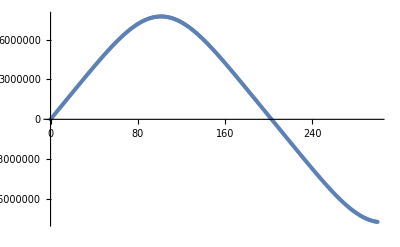

```mathematica
ListPlot[ data[[All, {5, 1}]]]
```

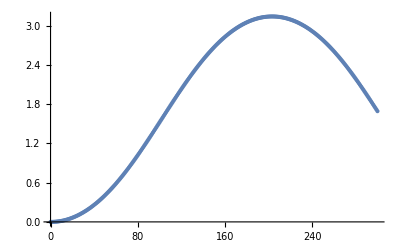

```mathematica
ListPlot[ data[[All, {5, 3}]]]
```

```mathematica
Manipulate[ListPlot[blub2[{ωc*α, 150}][[All, {5, 1}]], AxesLabel->{"n", "W"}],{α, 0.99, 1.01, 0.001}]
```